```mathematica
sel=Select[ExpressionToList[exps],Length[#]==2&]
```

{v1x26x345>0||v1x2x345x6>0,v1x256x34>0||v1x2x34x56>0,v1x2456x3>0||v1x2x3x456>0,v1x236x45>0||v1x23x45x6>0,v1x2356x4>0||v1x23x4x56>0,v1x2346x5>0||v1x234x5x6>0,v16x25x34>0||v16x2x34x5>0,v16x245x3>0||v16x2x3x45>0,v16x235x4>0||v16x23x4x5>0,v15x2346>0||v15x234x6>0,v156x24x3>0||v156x2x3x4>0,v15x234x6>0||v1x234x5x6>0,v15x2346>0||v1x2346x5>0,v14x2356>0||v14x23x56>0,v146x235>0||v146x23x5>0,v145x236>0||v145x23x6>0,v14x23x56>0||v1x23x4x56>0,v14x2356>0||v1x2356x4>0,v146x23x5>0||v16x23x4x5>0,v146x235>0||v16x235x4>0,v145x23x6>0||v1x23x45x6>0,v145x236>0||v1x236x45>0,v13x2456>0||v13x2x456>0,v136x245>0||v136x2x45>0,v1356x24>0||v1356x2x4>0,v134x256>0||v134x2x56>0,v1346x25>0||v1346x2x5>0,v1345x26>0||v1345x2x6>0,v13x2x456>0||v1x2x3x456>0,v13x2456>0||v1x2456x3>0,v136x2x45>0||v16x2x3x45>0,v136x245>0||v16x245x3>0,v1356x2x4>0||v156x2x3x4>0,v1356x24>0||v156x24x3>0,v134x2x56>0||v1x2x34x56>0,v134x256>0||v1x256x34>0,v1346x2x5>0||v16x2x34x5>0,v1346x25>0||v16x25x34>0,v1345x2x6>0||v1x2x345x6>0,v1345x26>0||v1x26x345>0,v12x36x45>0||v12x3x45x6>0,v12x356x4>0||v12x3x4x56>0,v12x346x5>0||v12x34x5x6>0,v126x35x4>0||v126x3x4x5>0,v125x346>0||v125x34x6>0,v125x34x6>0||v12x34x5x6>0,v125x346>0||v12x346x5>0,v124x356>0||v124x3x56>0,v1246x35>0||v1246x3x5>0,v1245x36>0||v1245x3x6>0,v124x3x56>0||v12x3x4x56>0,v124x356>0||v12x356x4>0,v1246x3x5>0||v126x3x4x5>0,v1246x35>0||v126x35x4>0,v1245x3x6>0||v12x3x45x6>0,v1245x36>0||v12x36x45>0,v123x46x5>0||v123x4x5x6>0,v1235x46>0||v1235x4x6>0,v1235x4x6>0||v123x4x5x6>0,v1235x46>0||v123x46x5>0}

```mathematica
Map[Length,ExpressionToList[exps]]//Tally//Sort
```

{{2,60},{3,246},{4,396},{5,821},{6,1011},{7,1278},{8,818},{9,1872},{10,1233},{11,837},{12,2658},{13,186},{14,2871},{15,1121},{16,774},{17,348},{18,2443},{19,1620},{20,516},{21,2028},{22,15},{23,174},{24,904},{25,180},{26,975},{27,2140},{28,360},{30,354},{31,60},{32,1170},{35,60},{36,1290},{40,72},{41,1296},{43,405},{48,240},{51,15},{55,1080},{58,45},{64,20},{74,435},{100,105},{136,15},{187,1}}

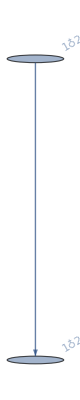
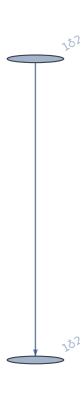
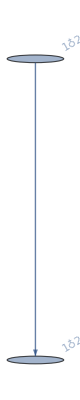
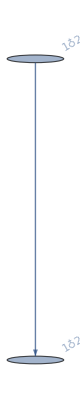
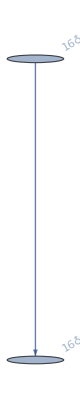
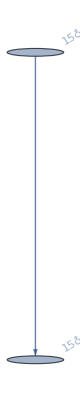
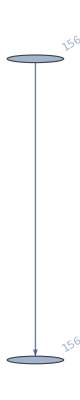
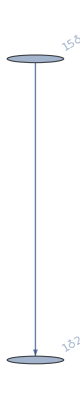
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[FormulaGraphReverse[ListofVars[#]]&,sel]
```

```mathematica
Map[If[HasTrianglePattern[#],SetsToSymbol[#,"v"],""]&,Map[SymbolToSets,DeleteDuplicates[sel//ListofVars]]]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
Sort[(sel//ListofVars//DeleteDuplicates),CompareSymbols]/.RepGraph6["C"]
```

{-Graphics-13571428,-Graphics-12017200,-Graphics-11957665,-Graphics-11957431,-Graphics-11957423,-Graphics-7410650,-Graphics-7253185,-Graphics-7233745,-Graphics-7233511,-Graphics-7200940,-Graphics-7194145,-Graphics-7194137,-Graphics-7174786,-Graphics-7174697,-Graphics-7174466,-Graphics-13750843,-Graphics-13571431,-Graphics-12674767,-Graphics-12555205,-Graphics-12495425,-Graphics-12136999,-Graphics-12017281,-Graphics-11957695,-Graphics-11957531,-Graphics-11957458,-Graphics-9477697,-Graphics-9359539,-Graphics-9300461,-Graphics-9005081,-Graphics-8827861,-Graphics-8768789,-Graphics-7902733,-Graphics-7784629,-Graphics-7725578,-Graphics-7417211,-Graphics-7378087,-Graphics-7255453,-Graphics-7242259,-Graphics-7235932,-Graphics-7201699,-Graphics-7197161,-Graphics-7194901,-Graphics-7183943,-Graphics-7177613,-Graphics-7175515,-Graphics-13750846,-Graphics-12674794,-Graphics-12555286,-Graphics-12495533,-Graphics-12137029,-Graphics-9478426,-Graphics-9361726,-Graphics-9303377,-Graphics-9011642,-Graphics-8836609,-Graphics-8778266,-Graphics-7903489,-Graphics-7786897,-Graphics-7728602,-Graphics-7378846}

```mathematica
SymbolToSets[v1345x26]//HasTrianglePattern
```

Part::partw: Part 3 of {{1,3,4,5},{2,6}} does not exist.

Intersection::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

True

```mathematica
sel//Length
```

60

```mathematica
Map[Length,ExpressionToList[Reduce[Fold[And,sel]]]]//Tally//Sort
```

{{30,32768}}

```mathematica
32768//FactorInteger
```

{{2,15}}

```mathematica
sel3=Select[ExpressionToList[exps],Length[#]==3&]
```

{v1x26x345>0||v1x2x3456>1||v1x2x345x6>0,v1x26x345>0||v1x26x34x5>0||v1x2x345x6>0,v1x26x345>0||v1x26x35x4>0||v1x2x345x6>0,v1x26x345>0||v1x26x3x45>0||v1x2x345x6>0,v1x256x34>0||v1x2x3456>1||v1x2x34x56>0,v1x256x34>0||v1x256x3x4>0||v1x2x34x56>0,v1x2456x3>0||v1x2x3456>1||v1x2x3x456>0,v1x236x45>0||v1x23x456>1||v1x23x45x6>0,v1x236x45>0||v1x236x4x5>0||v1x23x45x6>0,v1x2356x4>0||v1x23x456>1||v1x23x4x56>0,v1x2346x5>0||v1x234x56>1||v1x234x5x6>0,v1x2345x6>1||v1x2346x5>0||v1x234x5x6>0,v1x234x56>1||v1x2356x4>0||v1x23x4x56>0,v1x2345x6>1||v1x236x45>0||v1x23x45x6>0,v1x23x456>1||v1x2456x3>0||v1x2x3x456>0,v1x234x56>1||v1x256x34>0||v1x2x34x56>0,v1x2345x6>1||v1x26x345>0||v1x2x345x6>0,v16x25x34>0||v16x2x345>1||v16x2x34x5>0,v16x25x34>0||v16x25x3x4>0||v16x2x34x5>0,v16x245x3>0||v16x2x345>1||v16x2x3x45>0,v16x235x4>0||v16x23x45>1||v16x23x4x5>0,v16x234x5>1||v16x235x4>0||v16x23x4x5>0,v16x23x45>1||v16x245x3>0||v16x2x3x45>0,v16x234x5>1||v16x25x34>0||v16x2x34x5>0,v16x2x345>1||v1x26x345>0||v1x2x345x6>0,v16x25x34>0||v16x2x34x5>0||v1x25x34x6>0,v16x245x3>0||v16x2x3x45>0||v1x245x3x6>0,v16x23x45>1||v1x236x45>0||v1x23x45x6>0,v16x235x4>0||v16x23x4x5>0||v1x235x4x6>0,v16x234x5>1||v1x2346x5>0||v1x234x5x6>0,v15x26x34>0||v15x2x346>0||v15x2x34x6>0,v15x236x4>0||v15x23x46>0||v15x23x4x6>0,v156x24x3>0||v156x2x34>1||v156x2x3x4>0,v156x23x4>1||v156x24x3>0||v156x2x3x4>0,v156x24x3>0||v156x2x3x4>0||v15x24x3x6>0,v156x234>1||v15x2346>0||v15x234x6>0,v15x2x346>0||v1x25x346>0||v1x2x346x5>0,v15x23x46>0||v1x235x46>0||v1x23x46x5>0,v15x234x6>0||v1x234x56>1||v1x234x5x6>0,v15x234x6>0||v1x2345x6>1||v1x234x5x6>0,v15x2346>0||v1x23456>1||v1x2346x5>0,v15x234x6>0||v15x23x4x6>0||v1x234x5x6>0,v15x234x6>0||v15x24x3x6>0||v1x234x5x6>0,v15x234x6>0||v15x2x34x6>0||v1x234x5x6>0,v156x2x34>1||v16x25x34>0||v16x2x34x5>0,v156x24x3>0||v156x2x3x4>0||v16x24x3x5>0,v156x23x4>1||v16x235x4>0||v16x23x4x5>0,v156x2x34>1||v1x256x34>0||v1x2x34x56>0,v156x24x3>0||v156x2x3x4>0||v1x24x3x56>0,v156x23x4>1||v1x2356x4>0||v1x23x4x56>0,v15x234x6>0||v16x234x5>1||v1x234x5x6>0,v14x256x3>0||v14x2x356>0||v14x2x3x56>0,v14x235x6>0||v14x236x5>0||v14x23x5x6>0,v146x25x3>0||v146x2x35>0||v146x2x3x5>0,v145x26x3>0||v145x2x36>0||v145x2x3x6>0,v1456x23>1||v145x236>0||v145x23x6>0,v1456x23>1||v146x235>0||v146x23x5>0,v1456x23>1||v14x2356>0||v14x23x56>0,v14x2x356>0||v1x24x356>0||v1x2x356x4>0,v14x23x56>0||v14x23x5x6>0||v1x23x4x56>0,v14x23x56>0||v1x23x456>1||v1x23x4x56>0,v14x235x6>0||v1x235x46>0||v1x235x4x6>0,v14x23x56>0||v1x234x56>1||v1x23x4x56>0,v14x2356>0||v1x23456>1||v1x2356x4>0,v14x23x56>0||v14x2x3x56>0||v1x23x4x56>0,v146x2x35>0||v16x24x35>0||v16x2x35x4>0,v146x23x5>0||v16x23x45>1||v16x23x4x5>0,v146x23x5>0||v16x234x5>1||v16x23x4x5>0,v146x235>0||v16x2345>1||v16x235x4>0,v146x23x5>0||v146x2x3x5>0||v16x23x4x5>0,v1456x2x3>1||v156x24x3>0||v156x2x3x4>0,v145x2x36>0||v1x245x36>0||v1x2x36x45>0,v145x23x6>0||v1x23x456>1||v1x23x45x6>0,v14x236x5>0||v15x236x4>0||v1x236x4x5>0,v145x23x6>0||v1x2345x6>1||v1x23x45x6>0,v145x236>0||v1x23456>1||v1x236x45>0,v145x23x6>0||v145x2x3x6>0||v1x23x45x6>0,v1456x2x3>1||v16x245x3>0||v16x2x3x45>0,v146x23x5>0||v156x23x4>1||v16x23x4x5>0,v1456x2x3>1||v1x2456x3>0||v1x2x3x456>0,v14x23x56>0||v156x23x4>1||v1x23x4x56>0,v145x23x6>0||v16x23x45>1||v1x23x45x6>0,v13x24x56>0||v13x256x4>0||v13x2x4x56>0,v13x245x6>0||v13x26x45>0||v13x2x45x6>0,v136x24x5>0||v136x25x4>0||v136x2x4x5>0,v134x25x6>0||v134x26x5>0||v134x2x5x6>0,v13456x2>1||v1345x26>0||v1345x2x6>0,v13456x2>1||v1346x25>0||v1346x2x5>0,v13456x2>1||v134x256>0||v134x2x56>0,v13456x2>1||v1356x24>0||v1356x2x4>0,v13456x2>1||v136x245>0||v136x2x45>0,v13456x2>1||v13x2456>0||v13x2x456>0,v13x2x456>0||v13x2x45x6>0||v1x2x3x456>0,v13x2x456>0||v13x2x46x5>0||v1x2x3x456>0,v13x2x456>0||v13x2x4x56>0||v1x2x3x456>0,v13x2x456>0||v1x2x3456>1||v1x2x3x456>0,v13x24x56>0||v1x24x356>0||v1x24x3x56>0,v13x245x6>0||v1x245x36>0||v1x245x3x6>0,v13x2x456>0||v1x23x456>1||v1x2x3x456>0,v13x2456>0||v1x23456>1||v1x2456x3>0,v136x2x45>0||v136x2x4x5>0||v16x2x3x45>0,v136x2x45>0||v16x2x345>1||v16x2x3x45>0,v136x24x5>0||v16x24x35>0||v16x24x3x5>0,v136x2x45>0||v16x23x45>1||v16x2x3x45>0,v136x245>0||v16x2345>1||v16x245x3>0,v1356x2x4>0||v156x2x34>1||v156x2x3x4>0,v1356x2x4>0||v156x23x4>1||v156x2x3x4>0,v1356x24>0||v156x234>1||v156x24x3>0,v134x2x56>0||v134x2x5x6>0||v1x2x34x56>0,v134x2x56>0||v1x2x3456>1||v1x2x34x56>0,v134x25x6>0||v1x25x346>0||v1x25x34x6>0,v13x256x4>0||v14x256x3>0||v1x256x3x4>0,v134x2x56>0||v1x234x56>1||v1x2x34x56>0,v134x256>0||v1x23456>1||v1x256x34>0,v1346x2x5>0||v16x2x345>1||v16x2x34x5>0,v136x25x4>0||v146x25x3>0||v16x25x3x4>0,v1346x2x5>0||v16x234x5>1||v16x2x34x5>0,v1346x25>0||v16x2345>1||v16x25x34>0,v1356x2x4>0||v1456x2x3>1||v156x2x3x4>0,v1345x2x6>0||v1x2x3456>1||v1x2x345x6>0,v13x26x45>0||v145x26x3>0||v1x26x3x45>0,v134x26x5>0||v15x26x34>0||v1x26x34x5>0,v1345x2x6>0||v1x2345x6>1||v1x2x345x6>0,v1345x26>0||v1x23456>1||v1x26x345>0,v136x2x45>0||v1456x2x3>1||v16x2x3x45>0,v1346x2x5>0||v156x2x34>1||v16x2x34x5>0,v13x2x456>0||v1456x2x3>1||v1x2x3x456>0,v134x2x56>0||v156x2x34>1||v1x2x34x56>0,v1345x2x6>0||v16x2x345>1||v1x2x345x6>0,v12x36x45>0||v12x3x456>1||v12x3x45x6>0,v12x36x45>0||v12x36x4x5>0||v12x3x45x6>0,v12x356x4>0||v12x3x456>1||v12x3x4x56>0,v12x346x5>0||v12x34x56>1||v12x34x5x6>0,v12x345x6>1||v12x346x5>0||v12x34x5x6>0,v12x34x56>1||v12x356x4>0||v12x3x4x56>0,v12x345x6>1||v12x36x45>0||v12x3x45x6>0,v126x35x4>0||v126x3x45>1||v126x3x4x5>0,v126x34x5>1||v126x35x4>0||v126x3x4x5>0,v126x3x45>1||v12x36x45>0||v12x3x45x6>0,v126x35x4>0||v126x3x4x5>0||v12x35x4x6>0,v126x34x5>1||v12x346x5>0||v12x34x5x6>0,v125x36x4>0||v125x3x46>0||v125x3x4x6>0,v1256x34>1||v125x346>0||v125x34x6>0,v125x3x46>0||v12x35x46>0||v12x3x46x5>0,v125x34x6>0||v12x34x56>1||v12x34x5x6>0,v125x34x6>0||v12x345x6>1||v12x34x5x6>0,v125x346>0||v12x3456>1||v12x346x5>0,v125x34x6>0||v125x3x4x6>0||v12x34x5x6>0,v1256x3x4>1||v126x35x4>0||v126x3x4x5>0,v1256x3x4>1||v12x356x4>0||v12x3x4x56>0,v125x34x6>0||v126x34x5>1||v12x34x5x6>0,v124x35x6>0||v124x36x5>0||v124x3x5x6>0,v12456x3>1||v1245x36>0||v1245x3x6>0,v12456x3>1||v1246x35>0||v1246x3x5>0,v12456x3>1||v124x356>0||v124x3x56>0,v124x3x56>0||v124x3x5x6>0||v12x3x4x56>0,v124x3x56>0||v12x3x456>1||v12x3x4x56>0,v124x35x6>0||v12x35x46>0||v12x35x4x6>0,v124x3x56>0||v12x34x56>1||v12x3x4x56>0,v124x356>0||v12x3456>1||v12x356x4>0,v1246x3x5>0||v126x3x45>1||v126x3x4x5>0,v1246x3x5>0||v126x34x5>1||v126x3x4x5>0,v1246x35>0||v126x345>1||v126x35x4>0,v1245x3x6>0||v12x3x456>1||v12x3x45x6>0,v124x36x5>0||v125x36x4>0||v12x36x4x5>0,v1245x3x6>0||v12x345x6>1||v12x3x45x6>0,v1245x36>0||v12x3456>1||v12x36x45>0,v1246x3x5>0||v1256x3x4>1||v126x3x4x5>0,v124x3x56>0||v1256x3x4>1||v12x3x4x56>0,v1245x3x6>0||v126x3x45>1||v12x3x45x6>0,v123x46x5>0||v123x4x56>1||v123x4x5x6>0,v123x45x6>1||v123x46x5>0||v123x4x5x6>0,v1236x4x5>1||v123x46x5>0||v123x4x5x6>0,v12356x4>1||v1235x46>0||v1235x4x6>0,v1235x4x6>0||v123x4x56>1||v123x4x5x6>0,v1235x4x6>0||v123x45x6>1||v123x4x5x6>0,v1235x46>0||v123x456>1||v123x46x5>0,v1235x4x6>0||v1236x4x5>1||v123x4x5x6>0,v1234x5x6>1||v123x46x5>0||v123x4x5x6>0,v12345x6>1||v1235x46>0||v1235x4x6>0,v1234x5x6>1||v1235x4x6>0||v123x4x5x6>0,v12346x5>1||v1235x46>0||v123x46x5>0,v123x46x5>0||v123x4x5x6>0||v12x3x46x5>0,v123x45x6>1||v12x36x45>0||v12x3x45x6>0,v123x4x56>1||v12x356x4>0||v12x3x4x56>0,v1236x4x5>1||v126x35x4>0||v126x3x4x5>0,v1234x56>1||v124x356>0||v124x3x56>0,v12346x5>1||v1246x35>0||v1246x3x5>0,v12345x6>1||v1245x36>0||v1245x3x6>0,v123x4x56>1||v124x3x56>0||v12x3x4x56>0,v1234x5x6>1||v12x346x5>0||v12x34x5x6>0,v1236x4x5>1||v1246x3x5>0||v126x3x4x5>0,v12345x6>1||v125x346>0||v125x34x6>0,v123x45x6>1||v1245x3x6>0||v12x3x45x6>0,v1234x5x6>1||v125x34x6>0||v12x34x5x6>0,v12356x4>1||v1246x35>0||v126x35x4>0,v1236x45>1||v1245x36>0||v12x36x45>0,v12356x4>1||v124x356>0||v12x356x4>0,v12346x5>1||v125x346>0||v12x346x5>0,v12x36x45>0||v12x3x45x6>0||v1x2x36x45>0,v12x356x4>0||v12x3x4x56>0||v1x2x356x4>0,v12x346x5>0||v12x34x5x6>0||v1x2x346x5>0,v12x345x6>1||v1x26x345>0||v1x2x345x6>0,v12x34x56>1||v1x256x34>0||v1x2x34x56>0,v12x3x456>1||v1x2456x3>0||v1x2x3x456>0,v126x35x4>0||v126x3x4x5>0||v16x2x35x4>0,v126x34x5>1||v16x25x34>0||v16x2x34x5>0,v126x3x45>1||v16x245x3>0||v16x2x3x45>0,v126x35x4>0||v126x3x4x5>0||v1x26x35x4>0,v1256x3x4>1||v156x24x3>0||v156x2x3x4>0,v123x46x5>0||v123x4x5x6>0||v13x2x46x5>0,v123x456>1||v13x2456>0||v13x2x456>0,v1236x45>1||v136x245>0||v136x2x45>0,v12356x4>1||v1356x24>0||v1356x2x4>0,v1234x56>1||v134x256>0||v134x2x56>0,v12346x5>1||v1346x25>0||v1346x2x5>0,v12345x6>1||v1345x26>0||v1345x2x6>0,v12x3x456>1||v13x2x456>0||v1x2x3x456>0,v123x46x5>0||v123x4x5x6>0||v1x23x46x5>0,v123x45x6>1||v1x236x45>0||v1x23x45x6>0,v123x4x56>1||v1x2356x4>0||v1x23x4x56>0,v126x3x45>1||v136x2x45>0||v16x2x3x45>0,v1236x4x5>1||v16x235x4>0||v16x23x4x5>0,v1256x3x4>1||v1356x2x4>0||v156x2x3x4>0,v1234x56>1||v14x2356>0||v14x23x56>0,v12346x5>1||v146x235>0||v146x23x5>0,v12345x6>1||v145x236>0||v145x23x6>0,v12x34x56>1||v134x2x56>0||v1x2x34x56>0,v123x4x56>1||v14x23x56>0||v1x23x4x56>0,v1234x5x6>1||v1x2346x5>0||v1x234x5x6>0,v126x34x5>1||v1346x2x5>0||v16x2x34x5>0,v1236x4x5>1||v146x23x5>0||v16x23x4x5>0,v12345x6>1||v15x2346>0||v15x234x6>0,v12456x3>1||v1356x24>0||v156x24x3>0,v12x345x6>1||v1345x2x6>0||v1x2x345x6>0,v123x45x6>1||v145x23x6>0||v1x23x45x6>0,v1234x5x6>1||v15x234x6>0||v1x234x5x6>0,v1256x34>1||v1346x25>0||v16x25x34>0,v12456x3>1||v136x245>0||v16x245x3>0,v12356x4>1||v146x235>0||v16x235x4>0,v126x345>1||v1345x26>0||v1x26x345>0,v1256x34>1||v134x256>0||v1x256x34>0,v12456x3>1||v13x2456>0||v1x2456x3>0,v1236x45>1||v145x236>0||v1x236x45>0,v12356x4>1||v14x2356>0||v1x2356x4>0,v12346x5>1||v15x2346>0||v1x2346x5>0}

```mathematica
Map[FormulaGraphReverse[ListofVars[#]]&,sel3]
```

```mathematica
Map[Length,ExpressionToList[Reduce[Fold[And,sel3]]]]//Tally//Sort
```